# Graviton Basis Toolkit Validation Notebook

This notebook wraps the reproducible reducer validation stored in graviton_basis_toolkit_validation.wls. It is intended as the notebook counterpart to the script-based test run.

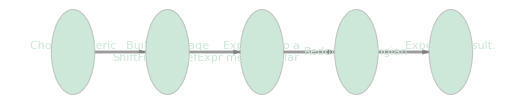

## Current Stored Results

The table below is loaded from graviton_basis_toolkit_validation_output.wl, which was produced by the most recent validation run.

Sector | IBPCount | RedefRank | PhysicalCount | DeltaBasisLength | LagTermCount | Reduced to 0?
{3,2} | 14 | 4 | 10 | 4 | 18 | True
{3,4} | 64 | 33 | 31 | 33 | 240 | True

## How to Re-run

Evaluate the following input cell from the notebook front end or run the corresponding script directly from the kernel.

```mathematica
Get["graviton_basis_toolkit_validation.wls"]
```

The script writes graviton_basis_toolkit_validation_output.wl and uses graviton_basis_validation_cache/ for sector caches.

## What the Validation Proves

It constructs Lagrangians that are in the image of a field redefinition of the Fierz-Pauli kinetic term.

It expands those images so they do not transparently look like EOM times delta h.

It runs ReduceLagrangian on the expanded expressions.

It checks that the reduced expression and all physical coordinates vanish.

## Useful Follow-up

```mathematica
Get["graviton_basis_toolkit_validation_output.wl"]
```

You can inspect the returned association directly, or compare the stored image coefficients against the redefinition basis of the relevant sector.